## Generate optimized energy, gradient, and Hessian expressions for molecular mechanics.

```mathematica
Directory[]
```

/Users/meister/Development/cando/extensions/cando/src/mathematica

```mathematica
SetDirectory["/Users/meister/Development/Cando/extensions/cando/src/mathematica"]
```

/Users/meister/Development/cando/extensions/cando/src/mathematica

## Setup to generate code that is embeded within CANDO

```mathematica
Needs["optimizeExpressions`"]
```

# Staple energy term

```mathematica
Clear[x1,y1,z1,x2,y2,z2];
```

```mathematica
myrot[a_,b_,c_,d_,x_,y_,z_]:= ({{a^2+b^2+c^2+d^2, 2*b*c-2*a*d, 2*b*d+2*a*c, x}, {2*b*c+2*a*d, a^2-b^2+c^2-d^2, 2*c*d-2*a*b, y}, {2*b*d-2*a*c, 2*c*d-2*a*b, a^2-b^2-c^2+d^2, z}, {0, 0, 0, 1}})
```

```mathematica
rotk = myrot[ak,bk,ck,dk,xk,yk,zk]
```

{{ak^2+bk^2+ck^2+dk^2,2 bk ck-2 ak dk,2 ak ck+2 bk dk,xk},{2 bk ck+2 ak dk,ak^2-bk^2+ck^2-dk^2,-2 ak bk+2 ck dk,yk},{-2 ak ck+2 bk dk,-2 ak bk+2 ck dk,ak^2-bk^2-ck^2+dk^2,zk},{0,0,0,1}}

```mathematica
rotl = myrot[al,bl,cl,dl,xl,yl,zl]
```

{{al^2+bl^2+cl^2+dl^2,2 bl cl-2 al dl,2 al cl+2 bl dl,xl},{2 bl cl+2 al dl,al^2-bl^2+cl^2-dl^2,-2 al bl+2 cl dl,yl},{-2 al cl+2 bl dl,-2 al bl+2 cl dl,al^2-bl^2-cl^2+dl^2,zl},{0,0,0,1}}

```mathematica
ba = { xh1, yh1, zh1 };
bb = { xh2, yh2, zh2 };
```

```mathematica
eba = Flatten[{ba,1}];
ebb = Flatten[{bb,1}];
```

```mathematica
stapleEnergyFn = (rotk.eba-rotl.ebb).(rotk.eba-rotl.ebb)
```

((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)^2+((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)^2+((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)^2

```mathematica
names = Flatten[{ba,bb}]
```

{xh1,yh1,zh1,xh2,yh2,zh2}

```mathematica
stapleVarNames = { 
{ak,a,I1,0},
{bk,b,I1,1},
{ck,c,I1,2},
{dk,d,I1,3},
{xk,x,I1,4},
{yk,y,I1,5},
{zk,z,I1,6},
{al,a,I2,0},
{bl,b,I2,1},
{cl,c,I2,2},
{dl,d,I2,3},
{xl,x,I2,4},
{yl,y,I2,5},
{zl,z,I2,6}
};
```

```mathematica
stapleSetupRules = {};
AppendTo[stapleSetupRules,CCode["STAPLE_SET_PARAMETER(I1,rigidBodyA);"]];
AppendTo[stapleSetupRules,CCode["STAPLE_SET_PARAMETER(I2,rigidBodyB);"]];
```

```mathematica
For[i=1,i≤Length[stapleVarNames],i++,
str = "STAPLE_SET_POSITION("<>ToString[stapleVarNames[[i]][[1]]]<>","<>ToString[stapleVarNames[[i]][[3]]]<>","<>ToString[stapleVarNames[[i]][[4]]]<>");";
(*Print[str];*)
AppendTo[stapleSetupRules,CCode[str]];
];
```

```mathematica
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(xh1,pointA,getX());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(yh1,pointA,getY());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(zh1,pointA,getZ());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(xh2,pointB,getX());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(yh2,pointB,getY());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(zh2,pointB,getZ());"]];
```

```mathematica
stapleSetupRules//MatrixForm
```

(CCode[STAPLE_SET_PARAMETER(I1,0);]
CCode[STAPLE_SET_PARAMETER(I2,2);]
CCode[STAPLE_SET_POSITION(ak,I1,0);]
CCode[STAPLE_SET_POSITION(bk,I1,1);]
CCode[STAPLE_SET_POSITION(ck,I1,2);]
CCode[STAPLE_SET_POSITION(dk,I1,3);]
CCode[STAPLE_SET_POSITION(xk,I1,4);]
CCode[STAPLE_SET_POSITION(yk,I1,5);]
CCode[STAPLE_SET_POSITION(zk,I1,6);]
CCode[STAPLE_SET_POSITION(al,I2,0);]
CCode[STAPLE_SET_POSITION(bl,I2,1);]
CCode[STAPLE_SET_POSITION(cl,I2,2);]
CCode[STAPLE_SET_POSITION(dl,I2,3);]
CCode[STAPLE_SET_POSITION(xl,I2,4);]
CCode[STAPLE_SET_POSITION(yl,I2,5);]
CCode[STAPLE_SET_POSITION(zl,I2,6);]
CCode[STAPLE_SET_POINT(xh1,1,0);]
CCode[STAPLE_SET_POINT(yh1,1,1);]
CCode[STAPLE_SET_POINT(zh1,1,2);]
CCode[STAPLE_SET_POINT(xh2,3,0);]
CCode[STAPLE_SET_POINT(yh2,3,1);]
CCode[STAPLE_SET_POINT(zh2,3,2);])

```mathematica
stapleEnergyRules = {};
stapleOutputs = {};
AppendTo[stapleEnergyRules,Assign[Energy,stapleEnergyFn]];
AppendTo[stapleEnergyRules,EnergyAccumulate["STAPLE",Energy]];
AppendTo[stapleOutputs,Energy];
```

## Append the Gradient rules

```mathematica
stapleEnergyFn
```

((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)^2+((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)^2+((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)^2

```mathematica
stapleForceRules = {};
```

```mathematica
AppendGradientAndForce["STAPLE",stapleEnergyRules,stapleOutputs,stapleEnergyFn,stapleVarNames];
```

```mathematica
stapleOutputs
```

{Energy,fak,fbk,fck,fdk,fxk,fyk,fzk,fal,fbl,fcl,fdl,fxl,fyl,fzl}

### Collect terms and convert to C code

```mathematica
stapleAllRules ={
stapleSetupRules,
stapleEnergyRules};
```

```mathematica
stapleRules = Flatten[stapleAllRules];
```

```mathematica
stapleRules
```

{CCode[STAPLE_SET_PARAMETER(I1,0);],CCode[STAPLE_SET_PARAMETER(I2,2);],CCode[STAPLE_SET_POSITION(ak,I1,0);],CCode[STAPLE_SET_POSITION(bk,I1,1);],CCode[STAPLE_SET_POSITION(ck,I1,2);],CCode[STAPLE_SET_POSITION(dk,I1,3);],CCode[STAPLE_SET_POSITION(xk,I1,4);],CCode[STAPLE_SET_POSITION(yk,I1,5);],CCode[STAPLE_SET_POSITION(zk,I1,6);],CCode[STAPLE_SET_POSITION(al,I2,0);],CCode[STAPLE_SET_POSITION(bl,I2,1);],CCode[STAPLE_SET_POSITION(cl,I2,2);],CCode[STAPLE_SET_POSITION(dl,I2,3);],CCode[STAPLE_SET_POSITION(xl,I2,4);],CCode[STAPLE_SET_POSITION(yl,I2,5);],CCode[STAPLE_SET_POSITION(zl,I2,6);],CCode[STAPLE_SET_POINT(xh1,1,0);],CCode[STAPLE_SET_POINT(yh1,1,1);],CCode[STAPLE_SET_POINT(zh1,1,2);],CCode[STAPLE_SET_POINT(xh2,3,0);],CCode[STAPLE_SET_POINT(yh2,3,1);],CCode[STAPLE_SET_POINT(zh2,3,2);],((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)^2+((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)^2+((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)^2→Energy,CCode[STAPLE_ENERGY_ACCUMULATE(Energy);],2 (2 ak xh1-2 dk yh1+2 ck zh1) ((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)+2 (2 dk xh1+2 ak yh1-2 bk zh1) ((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)+2 (-2 ck xh1-2 bk yh1+2 ak zh1) ((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)→gak,-gak→fak,CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );],2 (2 bk xh1+2 ck yh1+2 dk zh1) ((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)+2 (2 ck xh1-2 bk yh1-2 ak zh1) ((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)+2 (2 dk xh1-2 ak yh1-2 bk zh1) ((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)→gbk,-gbk→fbk,CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );],2 (2 ck xh1+2 bk yh1+2 ak zh1) ((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)+2 (2 bk xh1+2 ck yh1+2 dk zh1) ((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)+2 (-2 ak xh1+2 dk yh1-2 ck zh1) ((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)→gck,-gck→fck,CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );],2 (2 dk xh1-2 ak yh1+2 bk zh1) ((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)+2 (2 ak xh1-2 dk yh1+2 ck zh1) ((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)+2 (2 bk xh1+2 ck yh1+2 dk zh1) ((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)→gdk,-gdk→fdk,CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );],2 ((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)→gxk,-gxk→fxk,CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );],2 ((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)→gyk,-gyk→fyk,CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );],2 ((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)→gzk,-gzk→fzk,CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );],2 (-2 al xh2+2 dl yh2-2 cl zh2) ((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)+2 (-2 dl xh2-2 al yh2+2 bl zh2) ((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)+2 (2 cl xh2+2 bl yh2-2 al zh2) ((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)→gal,-gal→fal,CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );],2 (-2 bl xh2-2 cl yh2-2 dl zh2) ((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)+2 (-2 cl xh2+2 bl yh2+2 al zh2) ((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)+2 (-2 dl xh2+2 al yh2+2 bl zh2) ((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)→gbl,-gbl→fbl,CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );],2 (-2 cl xh2-2 bl yh2-2 al zh2) ((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)+2 (-2 bl xh2-2 cl yh2-2 dl zh2) ((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)+2 (2 al xh2-2 dl yh2+2 cl zh2) ((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)→gcl,-gcl→fcl,CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );],2 (-2 dl xh2+2 al yh2-2 bl zh2) ((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)+2 (-2 al xh2+2 dl yh2-2 cl zh2) ((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)+2 (-2 bl xh2-2 cl yh2-2 dl zh2) ((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)→gdl,-gdl→fdl,CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );],-2 ((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)→gxl,-gxl→fxl,CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );],-2 ((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)→gyl,-gyl→fyl,CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );],-2 ((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)→gzl,-gzl→fzl,CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]}

```mathematica
stapleInput = { ak,bk,ck,dk,xk,yk,zk, ak,bk,ck,dk,xk,yk,zk };
```

```mathematica
AppendTo[stapleOutputs,stapleDeviation];
```

### Assemble the rules, the name of the energy term, the independant variable names, etc. into what passes for a structure in Mathematica (I call it a Pack)

```mathematica
staplePack0 = {
Name->"STAPLE",
AdditionalCDeclares->"",
DerivativeVariables->{x1,y1,z1,x2,y2,z2},
Rules->stapleRules,
Input->stapleInput,
Output->stapleOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[staplePack0];
```

Writing finite difference debug code to: _STAPLE_debugFiniteDifference.cc

Writing debug variable declares to: _STAPLE_debugEvalDeclares.cc

Writing xml output debug code to: _STAPLE_debugEvalSerialize.cc

Writing set variables debug code to: _STAPLE_debugEvalSet.cc

staplePack = Block[{PrintTemporary = Print}, packOptimize[staplePack0]];

### Put the pedal to the metal and generate "C" code.

```mathematica
staplePack = packOptimize[staplePack0];
```

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null\ {Name → "STAPLE", AdditionalCDeclares → "", DerivativeVariables → {x1, y1, z1, x2, y2, z2}, Rules → {CCode["STAPLE_SET_PARAMETER(I1,0);"], CCode["STAPLE_SET_PARAMETER(I2,2);"], CCode["STAPLE_SET_POSITION(ak,I1,0);"], « 45 », 2\ Plus[« 3 »]\ Plus[« 8 »] + 2\ Plus[« 3 »]\ Plus[« 8 »] + 2\ Plus[« 3 »]\ Plus[« 8 »] → gbl, -gbl → fbl, « 16 »}, Input → {ak, bk, ck, dk, xk, yk, zk, ak, bk, ck, dk, xk, yk, zk}, Output → {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1,0);]

CCode[STAPLE_SET_PARAMETER(I2,2);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(xh1,1,0);]

CCode[STAPLE_SET_POINT(yh1,1,1);]

CCode[STAPLE_SET_POINT(zh1,1,2);]

CCode[STAPLE_SET_POINT(xh2,3,0);]

CCode[STAPLE_SET_POINT(yh2,3,1);]

CCode[STAPLE_SET_POINT(zh2,3,2);]

power2[bk] -> tx156

power2[bl] -> tx157

power2[ck] -> tx158

power2[cl] -> tx159

power2[dk] -> tx160

power2[dl] -> tx161

power2[ak] -> tx162

power2[al] -> tx163

-2. ak -> tzz313

bk tzz313 -> tx164

-2. al -> tzz312

bl tzz312 -> tx165

ck tzz313 -> tx166

2. ck -> tzz315

ak tzz315 -> tx167

bk tzz315 -> tx168

cl tzz312 -> tx169

2. cl -> tzz314

al tzz314 -> tx170

bl tzz314 -> tx171

dk tzz313 -> tx172

2. dk -> tzz311

ak tzz311 -> tx173

bk tzz311 -> tx174

ck tzz311 -> tx175

dl tzz312 -> tx176

2. al -> tzz319

dl tzz319 -> tx177

2. bl -> tzz320

dl tzz320 -> tx178

dl tzz314 -> tx179

-tx156 -> tx180

-tx157 -> tx181

-tx158 -> tx182

-tx159 -> tx183

-tx160 -> tx184

-tx161 -> tx185

tx156 + tx158 + tx160 + tx162 -> tx186

tx157 + tx159 + tx161 + tx163 -> tx187

tx168 + tx172 -> tx188

tx168 + tx173 -> tx189

tx166 + tx174 -> tx190

tx167 + tx174 -> tx191

tx164 + tx175 -> tx192

tx171 + tx176 -> tx193

tx171 + tx177 -> tx194

tx169 + tx178 -> tx195

tx170 + tx178 -> tx196

tx165 + tx179 -> tx197

tx160 + tx162 + tx180 + tx182 -> tx198

tx161 + tx163 + tx181 + tx183 -> tx199

tx158 + tx162 + tx180 + tx184 -> tx200

tx159 + tx163 + tx181 + tx185 -> tx201

tx186 xh1 -> tx202

tx189 xh1 -> tx203

tx190 xh1 -> tx204

-xh2 -> tzz325

tx187 tzz325 -> tx205

tx194 tzz325 -> tx206

tx195 tzz325 -> tx207

-xl -> tx208

tx188 yh1 -> tx209

tx192 yh1 -> tx210

tx200 yh1 -> tx211

-yh2 -> tzz324

tx193 tzz324 -> tx212

tx197 tzz324 -> tx213

tx201 tzz324 -> tx214

-yl -> tx215

tx191 zh1 -> tx216

tx192 zh1 -> tx217

tx198 zh1 -> tx218

-zh2 -> tzz323

tx196 tzz323 -> tx219

tx197 tzz323 -> tx220

tx199 tzz323 -> tx221

-zl -> tx222

tx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223

tx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224

tx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225

power2[tx223] -> tx226

power2[tx224] -> tx227

power2[tx225] -> tx228

tx226 + tx227 + tx228 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz322

tzz322 xh1 -> tx229

-2. ck xh1 -> tx230

tzz311 xh1 -> tx231

tzz322 yh1 -> tx232

-2. yh1 -> tzz330

bk tzz330 -> tx233

dk tzz330 -> tx234

tzz322 zh1 -> tx235

-2. zh1 -> tzz329

bk tzz329 -> tx236

tzz315 zh1 -> tx237

tx230 + tx233 + tx235 -> tx238

tx231 + tx232 + tx236 -> tx239

tx229 + tx234 + tx237 -> tx240

2. tx225 -> tzz316

tx238 tzz316 -> tx241

2. tx224 -> tzz317

tx239 tzz317 -> tx242

2. tx223 -> tzz318

tx240 tzz318 -> tx243

tx241 + tx242 + tx243 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz321

tzz321 xh1 -> tx244

tzz315 xh1 -> tx245

tzz313 yh1 -> tx246

tzz315 yh1 -> tx247

tzz313 zh1 -> tx248

tzz311 zh1 -> tx249

tx231 + tx236 + tx246 -> tx250

tx233 + tx245 + tx248 -> tx251

tx244 + tx247 + tx249 -> tx252

tx250 tzz316 -> tx253

tx251 tzz317 -> tx254

tx252 tzz318 -> tx255

tx253 + tx254 + tx255 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz313 xh1 -> tx256

tzz321 yh1 -> tx257

tzz311 yh1 -> tx258

ck tzz329 -> tx259

tx235 + tx245 + tx257 -> tx260

tx256 + tx258 + tx259 -> tx261

tx252 tzz317 -> tx262

tx260 tzz318 -> tx263

tx261 tzz316 -> tx264

tx262 + tx263 + tx264 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

tzz321 zh1 -> tx265

tx231 + tx246 + tx265 -> tx266

tx240 tzz317 -> tx267

tx252 tzz316 -> tx268

tx266 tzz318 -> tx269

tx267 + tx268 + tx269 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

tzz318 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tzz317 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tzz316 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz312 xh2 -> tx270

tzz314 xh2 -> tx271

-2. xh2 -> tzz328

dl tzz328 -> tx272

tzz312 yh2 -> tx273

tzz320 yh2 -> tx274

2. dl yh2 -> tx275

tzz312 zh2 -> tx276

tzz320 zh2 -> tx277

-2. zh2 -> tzz326

cl tzz326 -> tx278

tx271 + tx274 + tx276 -> tx279

tx272 + tx273 + tx277 -> tx280

tx270 + tx275 + tx278 -> tx281

gzk tx279 -> tx282

gyk tx280 -> tx283

gxk tx281 -> tx284

tx282 + tx283 + tx284 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz328 -> tx285

cl tzz328 -> tx286

tzz319 yh2 -> tx287

-2. yh2 -> tzz327

cl tzz327 -> tx288

tzz319 zh2 -> tx289

dl tzz326 -> tx290

tx272 + tx277 + tx287 -> tx291

tx274 + tx286 + tx289 -> tx292

tx285 + tx288 + tx290 -> tx293

gzk tx291 -> tx294

gyk tx292 -> tx295

gxk tx293 -> tx296

tx294 + tx295 + tx296 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz319 xh2 -> tx297

bl tzz327 -> tx298

dl tzz327 -> tx299

tzz314 zh2 -> tx300

tx276 + tx286 + tx298 -> tx301

tx297 + tx299 + tx300 -> tx302

gyk tx293 -> tx303

gxk tx301 -> tx304

gzk tx302 -> tx305

tx303 + tx304 + tx305 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz326 -> tx306

tx272 + tx287 + tx306 -> tx307

gyk tx281 -> tx308

gzk tx293 -> tx309

gxk tx307 -> tx310

tx308 + tx309 + tx310 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tx223 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

-2. tx224 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

-2. tx225 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

eliminateTrivialRules

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1,0);]

CCode[STAPLE_SET_PARAMETER(I2,2);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(xh1,1,0);]

CCode[STAPLE_SET_POINT(yh1,1,1);]

CCode[STAPLE_SET_POINT(zh1,1,2);]

CCode[STAPLE_SET_POINT(xh2,3,0);]

CCode[STAPLE_SET_POINT(yh2,3,1);]

CCode[STAPLE_SET_POINT(zh2,3,2);]

power2[bk] -> tx156

power2[bl] -> tx157

power2[ck] -> tx158

power2[cl] -> tx159

power2[dk] -> tx160

power2[dl] -> tx161

power2[ak] -> tx162

power2[al] -> tx163

-2. ak -> tzz313

bk tzz313 -> tx164

-2. al -> tzz312

bl tzz312 -> tx165

ck tzz313 -> tx166

2. ck -> tzz315

ak tzz315 -> tx167

bk tzz315 -> tx168

cl tzz312 -> tx169

2. cl -> tzz314

al tzz314 -> tx170

bl tzz314 -> tx171

dk tzz313 -> tx172

2. dk -> tzz311

ak tzz311 -> tx173

bk tzz311 -> tx174

ck tzz311 -> tx175

dl tzz312 -> tx176

2. al -> tzz319

dl tzz319 -> tx177

2. bl -> tzz320

dl tzz320 -> tx178

dl tzz314 -> tx179

-tx156 -> tx180

-tx157 -> tx181

-tx158 -> tx182

-tx159 -> tx183

-tx160 -> tx184

-tx161 -> tx185

tx156 + tx158 + tx160 + tx162 -> tx186

tx157 + tx159 + tx161 + tx163 -> tx187

tx168 + tx172 -> tx188

tx168 + tx173 -> tx189

tx166 + tx174 -> tx190

tx167 + tx174 -> tx191

tx164 + tx175 -> tx192

tx171 + tx176 -> tx193

tx171 + tx177 -> tx194

tx169 + tx178 -> tx195

tx170 + tx178 -> tx196

tx165 + tx179 -> tx197

tx160 + tx162 + tx180 + tx182 -> tx198

tx161 + tx163 + tx181 + tx183 -> tx199

tx158 + tx162 + tx180 + tx184 -> tx200

tx159 + tx163 + tx181 + tx185 -> tx201

tx186 xh1 -> tx202

tx189 xh1 -> tx203

tx190 xh1 -> tx204

-xh2 -> tzz325

tx187 tzz325 -> tx205

tx194 tzz325 -> tx206

tx195 tzz325 -> tx207

-xl -> tx208

tx188 yh1 -> tx209

tx192 yh1 -> tx210

tx200 yh1 -> tx211

-yh2 -> tzz324

tx193 tzz324 -> tx212

tx197 tzz324 -> tx213

tx201 tzz324 -> tx214

-yl -> tx215

tx191 zh1 -> tx216

tx192 zh1 -> tx217

tx198 zh1 -> tx218

-zh2 -> tzz323

tx196 tzz323 -> tx219

tx197 tzz323 -> tx220

tx199 tzz323 -> tx221

-zl -> tx222

tx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223

tx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224

tx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225

power2[tx223] -> tx226

power2[tx224] -> tx227

power2[tx225] -> tx228

tx226 + tx227 + tx228 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz322

tzz322 xh1 -> tx229

-2. ck xh1 -> tx230

tzz311 xh1 -> tx231

tzz322 yh1 -> tx232

-2. yh1 -> tzz330

bk tzz330 -> tx233

dk tzz330 -> tx234

tzz322 zh1 -> tx235

-2. zh1 -> tzz329

bk tzz329 -> tx236

tzz315 zh1 -> tx237

tx230 + tx233 + tx235 -> tx238

tx231 + tx232 + tx236 -> tx239

tx229 + tx234 + tx237 -> tx240

2. tx225 -> tzz316

tx238 tzz316 -> tx241

2. tx224 -> tzz317

tx239 tzz317 -> tx242

2. tx223 -> tzz318

tx240 tzz318 -> tx243

tx241 + tx242 + tx243 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz321

tzz321 xh1 -> tx244

tzz315 xh1 -> tx245

tzz313 yh1 -> tx246

tzz315 yh1 -> tx247

tzz313 zh1 -> tx248

tzz311 zh1 -> tx249

tx231 + tx236 + tx246 -> tx250

tx233 + tx245 + tx248 -> tx251

tx244 + tx247 + tx249 -> tx252

tx250 tzz316 -> tx253

tx251 tzz317 -> tx254

tx252 tzz318 -> tx255

tx253 + tx254 + tx255 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz313 xh1 -> tx256

tzz321 yh1 -> tx257

tzz311 yh1 -> tx258

ck tzz329 -> tx259

tx235 + tx245 + tx257 -> tx260

tx256 + tx258 + tx259 -> tx261

tx252 tzz317 -> tx262

tx260 tzz318 -> tx263

tx261 tzz316 -> tx264

tx262 + tx263 + tx264 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

tzz321 zh1 -> tx265

tx231 + tx246 + tx265 -> tx266

tx240 tzz317 -> tx267

tx252 tzz316 -> tx268

tx266 tzz318 -> tx269

tx267 + tx268 + tx269 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

tzz318 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tzz317 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tzz316 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz312 xh2 -> tx270

tzz314 xh2 -> tx271

-2. xh2 -> tzz328

dl tzz328 -> tx272

tzz312 yh2 -> tx273

tzz320 yh2 -> tx274

2. dl yh2 -> tx275

tzz312 zh2 -> tx276

tzz320 zh2 -> tx277

-2. zh2 -> tzz326

cl tzz326 -> tx278

tx271 + tx274 + tx276 -> tx279

tx272 + tx273 + tx277 -> tx280

tx270 + tx275 + tx278 -> tx281

gzk tx279 -> tx282

gyk tx280 -> tx283

gxk tx281 -> tx284

tx282 + tx283 + tx284 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz328 -> tx285

cl tzz328 -> tx286

tzz319 yh2 -> tx287

-2. yh2 -> tzz327

cl tzz327 -> tx288

tzz319 zh2 -> tx289

dl tzz326 -> tx290

tx272 + tx277 + tx287 -> tx291

tx274 + tx286 + tx289 -> tx292

tx285 + tx288 + tx290 -> tx293

gzk tx291 -> tx294

gyk tx292 -> tx295

gxk tx293 -> tx296

tx294 + tx295 + tx296 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz319 xh2 -> tx297

bl tzz327 -> tx298

dl tzz327 -> tx299

tzz314 zh2 -> tx300

tx276 + tx286 + tx298 -> tx301

tx297 + tx299 + tx300 -> tx302

gyk tx293 -> tx303

gxk tx301 -> tx304

gzk tx302 -> tx305

tx303 + tx304 + tx305 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz326 -> tx306

tx272 + tx287 + tx306 -> tx307

gyk tx281 -> tx308

gzk tx293 -> tx309

gxk tx307 -> tx310

tx308 + tx309 + tx310 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tx223 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

-2. tx224 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

-2. tx225 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1,0);]

CCode[STAPLE_SET_PARAMETER(I2,2);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(xh1,1,0);]

CCode[STAPLE_SET_POINT(yh1,1,1);]

CCode[STAPLE_SET_POINT(zh1,1,2);]

CCode[STAPLE_SET_POINT(xh2,3,0);]

CCode[STAPLE_SET_POINT(yh2,3,1);]

CCode[STAPLE_SET_POINT(zh2,3,2);]

power2[bk] -> tx156

power2[bl] -> tx157

power2[ck] -> tx158

power2[cl] -> tx159

power2[dk] -> tx160

power2[dl] -> tx161

power2[ak] -> tx162

power2[al] -> tx163

-2. ak -> tzz313

bk tzz313 -> tx164

-2. al -> tzz312

bl tzz312 -> tx165

ck tzz313 -> tx166

2. ck -> tzz315

ak tzz315 -> tx167

bk tzz315 -> tx168

cl tzz312 -> tx169

2. cl -> tzz314

al tzz314 -> tx170

bl tzz314 -> tx171

dk tzz313 -> tx172

2. dk -> tzz311

ak tzz311 -> tx173

bk tzz311 -> tx174

ck tzz311 -> tx175

dl tzz312 -> tx176

2. al -> tzz319

dl tzz319 -> tx177

2. bl -> tzz320

dl tzz320 -> tx178

dl tzz314 -> tx179

-tx156 -> tx180

-tx157 -> tx181

-tx158 -> tx182

-tx159 -> tx183

-tx160 -> tx184

-tx161 -> tx185

tx156 + tx158 + tx160 + tx162 -> tx186

tx157 + tx159 + tx161 + tx163 -> tx187

tx168 + tx172 -> tx188

tx168 + tx173 -> tx189

tx166 + tx174 -> tx190

tx167 + tx174 -> tx191

tx164 + tx175 -> tx192

tx171 + tx176 -> tx193

tx171 + tx177 -> tx194

tx169 + tx178 -> tx195

tx170 + tx178 -> tx196

tx165 + tx179 -> tx197

tx162 + tx180 -> tzz334

tx160 + tx182 + tzz334 -> tx198

tx163 + tx181 -> tzz333

tx161 + tx183 + tzz333 -> tx199

tx158 + tx184 + tzz334 -> tx200

tx159 + tx185 + tzz333 -> tx201

tx186 xh1 -> tx202

tx189 xh1 -> tx203

tx190 xh1 -> tx204

-xh2 -> tzz325

tx187 tzz325 -> tx205

tx194 tzz325 -> tx206

tx195 tzz325 -> tx207

-xl -> tx208

tx188 yh1 -> tx209

tx192 yh1 -> tx210

tx200 yh1 -> tx211

-yh2 -> tzz324

tx193 tzz324 -> tx212

tx197 tzz324 -> tx213

tx201 tzz324 -> tx214

-yl -> tx215

tx191 zh1 -> tx216

tx192 zh1 -> tx217

tx198 zh1 -> tx218

-zh2 -> tzz323

tx196 tzz323 -> tx219

tx197 tzz323 -> tx220

tx199 tzz323 -> tx221

-zl -> tx222

tx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223

tx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224

tx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225

power2[tx223] -> tx226

power2[tx224] -> tx227

power2[tx225] -> tx228

tx226 + tx227 + tx228 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz322

tzz322 xh1 -> tx229

-2. ck xh1 -> tx230

tzz311 xh1 -> tx231

tzz322 yh1 -> tx232

-2. yh1 -> tzz330

bk tzz330 -> tx233

dk tzz330 -> tx234

tzz322 zh1 -> tx235

-2. zh1 -> tzz329

bk tzz329 -> tx236

tzz315 zh1 -> tx237

tx230 + tx233 + tx235 -> tx238

tx231 + tx232 + tx236 -> tx239

tx229 + tx234 + tx237 -> tx240

2. tx225 -> tzz316

tx238 tzz316 -> tx241

2. tx224 -> tzz317

tx239 tzz317 -> tx242

2. tx223 -> tzz318

tx240 tzz318 -> tx243

tx241 + tx242 + tx243 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz321

tzz321 xh1 -> tx244

tzz315 xh1 -> tx245

tzz313 yh1 -> tx246

tzz315 yh1 -> tx247

tzz313 zh1 -> tx248

tzz311 zh1 -> tx249

tx231 + tx246 -> tzz332

tx236 + tzz332 -> tx250

tx233 + tx245 + tx248 -> tx251

tx244 + tx247 + tx249 -> tx252

tx250 tzz316 -> tx253

tx251 tzz317 -> tx254

tx252 tzz318 -> tx255

tx253 + tx254 + tx255 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz313 xh1 -> tx256

tzz321 yh1 -> tx257

tzz311 yh1 -> tx258

ck tzz329 -> tx259

tx235 + tx245 + tx257 -> tx260

tx256 + tx258 + tx259 -> tx261

tx252 tzz317 -> tx262

tx260 tzz318 -> tx263

tx261 tzz316 -> tx264

tx262 + tx263 + tx264 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

tzz321 zh1 -> tx265

tx265 + tzz332 -> tx266

tx240 tzz317 -> tx267

tx252 tzz316 -> tx268

tx266 tzz318 -> tx269

tx267 + tx268 + tx269 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

tzz318 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tzz317 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tzz316 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz312 xh2 -> tx270

tzz314 xh2 -> tx271

-2. xh2 -> tzz328

dl tzz328 -> tx272

tzz312 yh2 -> tx273

tzz320 yh2 -> tx274

2. dl yh2 -> tx275

tzz312 zh2 -> tx276

tzz320 zh2 -> tx277

-2. zh2 -> tzz326

cl tzz326 -> tx278

tx271 + tx274 + tx276 -> tx279

tx272 + tx273 + tx277 -> tx280

tx270 + tx275 + tx278 -> tx281

gzk tx279 -> tx282

gyk tx280 -> tx283

gxk tx281 -> tx284

tx282 + tx283 + tx284 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz328 -> tx285

cl tzz328 -> tx286

tzz319 yh2 -> tx287

-2. yh2 -> tzz327

cl tzz327 -> tx288

tzz319 zh2 -> tx289

dl tzz326 -> tx290

tx272 + tx287 -> tzz331

tx277 + tzz331 -> tx291

tx274 + tx286 + tx289 -> tx292

tx285 + tx288 + tx290 -> tx293

gzk tx291 -> tx294

gyk tx292 -> tx295

gxk tx293 -> tx296

tx294 + tx295 + tx296 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz319 xh2 -> tx297

bl tzz327 -> tx298

dl tzz327 -> tx299

tzz314 zh2 -> tx300

tx276 + tx286 + tx298 -> tx301

tx297 + tx299 + tx300 -> tx302

gyk tx293 -> tx303

gxk tx301 -> tx304

gzk tx302 -> tx305

tx303 + tx304 + tx305 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz326 -> tx306

tx306 + tzz331 -> tx307

gyk tx281 -> tx308

gzk tx293 -> tx309

gxk tx307 -> tx310

tx308 + tx309 + tx310 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tx223 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

-2. tx224 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

-2. tx225 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

Writing declares to file: _STAPLE_termDeclares.cc

Writing code to file: _STAPLE_termCode.cc

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null\ {Name → "CONNECT", AdditionalCDeclares → "", DerivativeVariables → {x1, y1, z1, x2, y2, z2}, Rules → {CCode["CONNECT_SET_PARAMETER(I1);"], CCode["CONNECT_SET_PARAMETER(I2);"], CCode["CONNECT_SET_POSITION(ak,I1,0);"], « 45 », 2\ Plus[« 3 »]\ Plus[« 8 »] + 2\ Plus[« 3 »]\ Plus[« 8 »] + 2\ Plus[« 3 »]\ Plus[« 8 »] → gdl, -gdl → fdl, « 10 »}, Input → {ak, bk, ck, dk, xk, yk, zk, ak, bk, ck, dk, xk, yk, zk}, Output → {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, connectDeviation}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1);]\n\nCCode[STAPLE_SET_PARAMETER(I2);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\npower2[bk] -> tx156\n\npower2[bl] -> tx157\n\npower2[ck] -> tx158\n\npower2[cl] -> tx159\n\npower2[dk] -> tx160\n\npower2[dl] -> tx161\n\npower2[ak] -> tx162\n\npower2[al] -> tx163\n\n-2. ak -> tzz313\n\nbk tzz313 -> tx164\n\n-2. al -> tzz312\n\nbl tzz312 -> tx165\n\nck tzz313 -> tx166\n\n2. ck -> tzz315\n\nak tzz315 -> tx167\n\nbk tzz315 -> tx168\n\ncl tzz312 -> tx169\n\n2. cl -> tzz314\n\nal tzz314 -> tx170\n\nbl tzz314 -> tx171\n\ndk tzz313 -> tx172\n\n2. dk -> tzz311\n\nak tzz311 -> tx173\n\nbk tzz311 -> tx174\n\nck tzz311 -> tx175\n\ndl tzz312 -> tx176\n\n2. al -> tzz319\n\ndl tzz319 -> tx177\n\n2. bl -> tzz320\n\ndl tzz320 -> tx178\n\ndl tzz314 -> tx179\n\n-tx156 -> tx180\n\n-tx157 -> tx181\n\n-tx158 -> tx182\n\n-tx159 -> tx183\n\n-tx160 -> tx184\n\n-tx161 -> tx185\n\ntx156 + tx158 + tx160 + tx162 -> tx186\n\ntx157 + tx159 + tx161 + tx163 -> tx187\n\ntx168 + tx172 -> tx188\n\ntx168 + tx173 -> tx189\n\ntx166 + tx174 -> tx190\n\ntx167 + tx174 -> tx191\n\ntx164 + tx175 -> tx192\n\ntx171 + tx176 -> tx193\n\ntx171 + tx177 -> tx194\n\ntx169 + tx178 -> tx195\n\ntx170 + tx178 -> tx196\n\ntx165 + tx179 -> tx197\n\ntx160 + tx162 + tx180 + tx182 -> tx198\n\ntx161 + tx163 + tx181 + tx183 -> tx199\n\ntx158 + tx162 + tx180 + tx184 -> tx200\n\ntx159 + tx163 + tx181 + tx185 -> tx201\n\ntx186 x1 -> tx202\n\ntx189 x1 -> tx203\n\ntx190 x1 -> tx204\n\n-x2 -> tzz325\n\ntx187 tzz325 -> tx205\n\ntx194 tzz325 -> tx206\n\ntx195 tzz325 -> tx207\n\n-xl -> tx208\n\ntx188 y1 -> tx209\n\ntx192 y1 -> tx210\n\ntx200 y1 -> tx211\n\n-y2 -> tzz324\n\ntx193 tzz324 -> tx212\n\ntx197 tzz324 -> tx213\n\ntx201 tzz324 -> tx214\n\n-yl -> tx215\n\ntx191 z1 -> tx216\n\ntx192 z1 -> tx217\n\ntx198 z1 -> tx218\n\n-z2 -> tzz323\n\ntx196 tzz323 -> tx219\n\ntx197 tzz323 -> tx220\n\ntx199 tzz323 -> tx221\n\n-zl -> tx222\n\ntx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223\n\ntx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224\n\ntx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225\n\npower2[tx223] -> tx226\n\npower2[tx224] -> tx227\n\npower2[tx225] -> tx228\n\ntx226 + tx227 + tx228 -> Energy\n\nCCode[staple_ENERGY_ACCUMULATE(Energy);]\n\n2. ak -> tzz322\n\ntzz322 x1 -> tx229\n\n-2. ck x1 -> tx230\n\ntzz311 x1 -> tx231\n\ntzz322 y1 -> tx232\n\n-2. y1 -> tzz330\n\nbk tzz330 -> tx233\n\ndk tzz330 -> tx234\n\ntzz322 z1 -> tx235\n\n-2. z1 -> tzz329\n\nbk tzz329 -> tx236\n\ntzz315 z1 -> tx237\n\ntx230 + tx233 + tx235 -> tx238\n\ntx231 + tx232 + tx236 -> tx239\n\ntx229 + tx234 + tx237 -> tx240\n\n2. tx225 -> tzz316\n\ntx238 tzz316 -> tx241\n\n2. tx224 -> tzz317\n\ntx239 tzz317 -> tx242\n\n2. tx223 -> tzz318\n\ntx240 tzz318 -> tx243\n\ntx241 + tx242 + tx243 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\n2. bk -> tzz321\n\ntzz321 x1 -> tx244\n\ntzz315 x1 -> tx245\n\ntzz313 y1 -> tx246\n\ntzz315 y1 -> tx247\n\ntzz313 z1 -> tx248\n\ntzz311 z1 -> tx249\n\ntx231 + tx236 + tx246 -> tx250\n\ntx233 + tx245 + tx248 -> tx251\n\ntx244 + tx247 + tx249 -> tx252\n\ntx250 tzz316 -> tx253\n\ntx251 tzz317 -> tx254\n\ntx252 tzz318 -> tx255\n\ntx253 + tx254 + tx255 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\ntzz313 x1 -> tx256\n\ntzz321 y1 -> tx257\n\ntzz311 y1 -> tx258\n\nck tzz329 -> tx259\n\ntx235 + tx245 + tx257 -> tx260\n\ntx256 + tx258 + tx259 -> tx261\n\ntx252 tzz317 -> tx262\n\ntx260 tzz318 -> tx263\n\ntx261 tzz316 -> tx264\n\ntx262 + tx263 + tx264 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\ntzz321 z1 -> tx265\n\ntx231 + tx246 + tx265 -> tx266\n\ntx240 tzz317 -> tx267\n\ntx252 tzz316 -> tx268\n\ntx266 tzz318 -> tx269\n\ntx267 + tx268 + tx269 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz318 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz317 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz316 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz312 x2 -> tx270\n\ntzz314 x2 -> tx271\n\n-2. x2 -> tzz328\n\ndl tzz328 -> tx272\n\ntzz312 y2 -> tx273\n\ntzz320 y2 -> tx274\n\n2. dl y2 -> tx275\n\ntzz312 z2 -> tx276\n\ntzz320 z2 -> tx277\n\n-2. z2 -> tzz326\n\ncl tzz326 -> tx278\n\ntx271 + tx274 + tx276 -> tx279\n\ntx272 + tx273 + tx277 -> tx280\n\ntx270 + tx275 + tx278 -> tx281\n\ngzk tx279 -> tx282\n\ngyk tx280 -> tx283\n\ngxk tx281 -> tx284\n\ntx282 + tx283 + tx284 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\nbl tzz328 -> tx285\n\ncl tzz328 -> tx286\n\ntzz319 y2 -> tx287\n\n-2. y2 -> tzz327\n\ncl tzz327 -> tx288\n\ntzz319 z2 -> tx289\n\ndl tzz326 -> tx290\n\ntx272 + tx277 + tx287 -> tx291\n\ntx274 + tx286 + tx289 -> tx292\n\ntx285 + tx288 + tx290 -> tx293\n\ngzk tx291 -> tx294\n\ngyk tx292 -> tx295\n\ngxk tx293 -> tx296\n\ntx294 + tx295 + tx296 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\ntzz319 x2 -> tx297\n\nbl tzz327 -> tx298\n\ndl tzz327 -> tx299\n\ntzz314 z2 -> tx300\n\ntx276 + tx286 + tx298 -> tx301\n\ntx297 + tx299 + tx300 -> tx302\n\ngyk tx293 -> tx303\n\ngxk tx301 -> tx304\n\ngzk tx302 -> tx305\n\ntx303 + tx304 + tx305 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nbl tzz326 -> tx306\n\ntx272 + tx287 + tx306 -> tx307\n\ngyk tx281 -> tx308\n\ngzk tx293 -> tx309\n\ngxk tx307 -> tx310\n\ntx308 + tx309 + tx310 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tx223 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\n-2. tx224 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\n-2. tx225 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

eliminateTrivialRules

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1);]\n\nCCode[STAPLE_SET_PARAMETER(I2);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\npower2[bk] -> tx156\n\npower2[bl] -> tx157\n\npower2[ck] -> tx158\n\npower2[cl] -> tx159\n\npower2[dk] -> tx160\n\npower2[dl] -> tx161\n\npower2[ak] -> tx162\n\npower2[al] -> tx163\n\n-2. ak -> tzz313\n\nbk tzz313 -> tx164\n\n-2. al -> tzz312\n\nbl tzz312 -> tx165\n\nck tzz313 -> tx166\n\n2. ck -> tzz315\n\nak tzz315 -> tx167\n\nbk tzz315 -> tx168\n\ncl tzz312 -> tx169\n\n2. cl -> tzz314\n\nal tzz314 -> tx170\n\nbl tzz314 -> tx171\n\ndk tzz313 -> tx172\n\n2. dk -> tzz311\n\nak tzz311 -> tx173\n\nbk tzz311 -> tx174\n\nck tzz311 -> tx175\n\ndl tzz312 -> tx176\n\n2. al -> tzz319\n\ndl tzz319 -> tx177\n\n2. bl -> tzz320\n\ndl tzz320 -> tx178\n\ndl tzz314 -> tx179\n\n-tx156 -> tx180\n\n-tx157 -> tx181\n\n-tx158 -> tx182\n\n-tx159 -> tx183\n\n-tx160 -> tx184\n\n-tx161 -> tx185\n\ntx156 + tx158 + tx160 + tx162 -> tx186\n\ntx157 + tx159 + tx161 + tx163 -> tx187\n\ntx168 + tx172 -> tx188\n\ntx168 + tx173 -> tx189\n\ntx166 + tx174 -> tx190\n\ntx167 + tx174 -> tx191\n\ntx164 + tx175 -> tx192\n\ntx171 + tx176 -> tx193\n\ntx171 + tx177 -> tx194\n\ntx169 + tx178 -> tx195\n\ntx170 + tx178 -> tx196\n\ntx165 + tx179 -> tx197\n\ntx160 + tx162 + tx180 + tx182 -> tx198\n\ntx161 + tx163 + tx181 + tx183 -> tx199\n\ntx158 + tx162 + tx180 + tx184 -> tx200\n\ntx159 + tx163 + tx181 + tx185 -> tx201\n\ntx186 x1 -> tx202\n\ntx189 x1 -> tx203\n\ntx190 x1 -> tx204\n\n-x2 -> tzz325\n\ntx187 tzz325 -> tx205\n\ntx194 tzz325 -> tx206\n\ntx195 tzz325 -> tx207\n\n-xl -> tx208\n\ntx188 y1 -> tx209\n\ntx192 y1 -> tx210\n\ntx200 y1 -> tx211\n\n-y2 -> tzz324\n\ntx193 tzz324 -> tx212\n\ntx197 tzz324 -> tx213\n\ntx201 tzz324 -> tx214\n\n-yl -> tx215\n\ntx191 z1 -> tx216\n\ntx192 z1 -> tx217\n\ntx198 z1 -> tx218\n\n-z2 -> tzz323\n\ntx196 tzz323 -> tx219\n\ntx197 tzz323 -> tx220\n\ntx199 tzz323 -> tx221\n\n-zl -> tx222\n\ntx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223\n\ntx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224\n\ntx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225\n\npower2[tx223] -> tx226\n\npower2[tx224] -> tx227\n\npower2[tx225] -> tx228\n\ntx226 + tx227 + tx228 -> Energy\n\nCCode[staple_ENERGY_ACCUMULATE(Energy);]\n\n2. ak -> tzz322\n\ntzz322 x1 -> tx229\n\n-2. ck x1 -> tx230\n\ntzz311 x1 -> tx231\n\ntzz322 y1 -> tx232\n\n-2. y1 -> tzz330\n\nbk tzz330 -> tx233\n\ndk tzz330 -> tx234\n\ntzz322 z1 -> tx235\n\n-2. z1 -> tzz329\n\nbk tzz329 -> tx236\n\ntzz315 z1 -> tx237\n\ntx230 + tx233 + tx235 -> tx238\n\ntx231 + tx232 + tx236 -> tx239\n\ntx229 + tx234 + tx237 -> tx240\n\n2. tx225 -> tzz316\n\ntx238 tzz316 -> tx241\n\n2. tx224 -> tzz317\n\ntx239 tzz317 -> tx242\n\n2. tx223 -> tzz318\n\ntx240 tzz318 -> tx243\n\ntx241 + tx242 + tx243 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\n2. bk -> tzz321\n\ntzz321 x1 -> tx244\n\ntzz315 x1 -> tx245\n\ntzz313 y1 -> tx246\n\ntzz315 y1 -> tx247\n\ntzz313 z1 -> tx248\n\ntzz311 z1 -> tx249\n\ntx231 + tx236 + tx246 -> tx250\n\ntx233 + tx245 + tx248 -> tx251\n\ntx244 + tx247 + tx249 -> tx252\n\ntx250 tzz316 -> tx253\n\ntx251 tzz317 -> tx254\n\ntx252 tzz318 -> tx255\n\ntx253 + tx254 + tx255 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\ntzz313 x1 -> tx256\n\ntzz321 y1 -> tx257\n\ntzz311 y1 -> tx258\n\nck tzz329 -> tx259\n\ntx235 + tx245 + tx257 -> tx260\n\ntx256 + tx258 + tx259 -> tx261\n\ntx252 tzz317 -> tx262\n\ntx260 tzz318 -> tx263\n\ntx261 tzz316 -> tx264\n\ntx262 + tx263 + tx264 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\ntzz321 z1 -> tx265\n\ntx231 + tx246 + tx265 -> tx266\n\ntx240 tzz317 -> tx267\n\ntx252 tzz316 -> tx268\n\ntx266 tzz318 -> tx269\n\ntx267 + tx268 + tx269 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz318 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz317 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz316 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz312 x2 -> tx270\n\ntzz314 x2 -> tx271\n\n-2. x2 -> tzz328\n\ndl tzz328 -> tx272\n\ntzz312 y2 -> tx273\n\ntzz320 y2 -> tx274\n\n2. dl y2 -> tx275\n\ntzz312 z2 -> tx276\n\ntzz320 z2 -> tx277\n\n-2. z2 -> tzz326\n\ncl tzz326 -> tx278\n\ntx271 + tx274 + tx276 -> tx279\n\ntx272 + tx273 + tx277 -> tx280\n\ntx270 + tx275 + tx278 -> tx281\n\ngzk tx279 -> tx282\n\ngyk tx280 -> tx283\n\ngxk tx281 -> tx284\n\ntx282 + tx283 + tx284 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\nbl tzz328 -> tx285\n\ncl tzz328 -> tx286\n\ntzz319 y2 -> tx287\n\n-2. y2 -> tzz327\n\ncl tzz327 -> tx288\n\ntzz319 z2 -> tx289\n\ndl tzz326 -> tx290\n\ntx272 + tx277 + tx287 -> tx291\n\ntx274 + tx286 + tx289 -> tx292\n\ntx285 + tx288 + tx290 -> tx293\n\ngzk tx291 -> tx294\n\ngyk tx292 -> tx295\n\ngxk tx293 -> tx296\n\ntx294 + tx295 + tx296 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\ntzz319 x2 -> tx297\n\nbl tzz327 -> tx298\n\ndl tzz327 -> tx299\n\ntzz314 z2 -> tx300\n\ntx276 + tx286 + tx298 -> tx301\n\ntx297 + tx299 + tx300 -> tx302\n\ngyk tx293 -> tx303\n\ngxk tx301 -> tx304\n\ngzk tx302 -> tx305\n\ntx303 + tx304 + tx305 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nbl tzz326 -> tx306\n\ntx272 + tx287 + tx306 -> tx307\n\ngyk tx281 -> tx308\n\ngzk tx293 -> tx309\n\ngxk tx307 -> tx310\n\ntx308 + tx309 + tx310 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tx223 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\n-2. tx224 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\n-2. tx225 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1);]\n\nCCode[STAPLE_SET_PARAMETER(I2);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\npower2[bk] -> tx156\n\npower2[bl] -> tx157\n\npower2[ck] -> tx158\n\npower2[cl] -> tx159\n\npower2[dk] -> tx160\n\npower2[dl] -> tx161\n\npower2[ak] -> tx162\n\npower2[al] -> tx163\n\n-2. ak -> tzz313\n\nbk tzz313 -> tx164\n\n-2. al -> tzz312\n\nbl tzz312 -> tx165\n\nck tzz313 -> tx166\n\n2. ck -> tzz315\n\nak tzz315 -> tx167\n\nbk tzz315 -> tx168\n\ncl tzz312 -> tx169\n\n2. cl -> tzz314\n\nal tzz314 -> tx170\n\nbl tzz314 -> tx171\n\ndk tzz313 -> tx172\n\n2. dk -> tzz311\n\nak tzz311 -> tx173\n\nbk tzz311 -> tx174\n\nck tzz311 -> tx175\n\ndl tzz312 -> tx176\n\n2. al -> tzz319\n\ndl tzz319 -> tx177\n\n2. bl -> tzz320\n\ndl tzz320 -> tx178\n\ndl tzz314 -> tx179\n\n-tx156 -> tx180\n\n-tx157 -> tx181\n\n-tx158 -> tx182\n\n-tx159 -> tx183\n\n-tx160 -> tx184\n\n-tx161 -> tx185\n\ntx156 + tx158 + tx160 + tx162 -> tx186\n\ntx157 + tx159 + tx161 + tx163 -> tx187\n\ntx168 + tx172 -> tx188\n\ntx168 + tx173 -> tx189\n\ntx166 + tx174 -> tx190\n\ntx167 + tx174 -> tx191\n\ntx164 + tx175 -> tx192\n\ntx171 + tx176 -> tx193\n\ntx171 + tx177 -> tx194\n\ntx169 + tx178 -> tx195\n\ntx170 + tx178 -> tx196\n\ntx165 + tx179 -> tx197\n\ntx162 + tx180 -> tzz334\n\ntx160 + tx182 + tzz334 -> tx198\n\ntx163 + tx181 -> tzz333\n\ntx161 + tx183 + tzz333 -> tx199\n\ntx158 + tx184 + tzz334 -> tx200\n\ntx159 + tx185 + tzz333 -> tx201\n\ntx186 x1 -> tx202\n\ntx189 x1 -> tx203\n\ntx190 x1 -> tx204\n\n-x2 -> tzz325\n\ntx187 tzz325 -> tx205\n\ntx194 tzz325 -> tx206\n\ntx195 tzz325 -> tx207\n\n-xl -> tx208\n\ntx188 y1 -> tx209\n\ntx192 y1 -> tx210\n\ntx200 y1 -> tx211\n\n-y2 -> tzz324\n\ntx193 tzz324 -> tx212\n\ntx197 tzz324 -> tx213\n\ntx201 tzz324 -> tx214\n\n-yl -> tx215\n\ntx191 z1 -> tx216\n\ntx192 z1 -> tx217\n\ntx198 z1 -> tx218\n\n-z2 -> tzz323\n\ntx196 tzz323 -> tx219\n\ntx197 tzz323 -> tx220\n\ntx199 tzz323 -> tx221\n\n-zl -> tx222\n\ntx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223\n\ntx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224\n\ntx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225\n\npower2[tx223] -> tx226\n\npower2[tx224] -> tx227\n\npower2[tx225] -> tx228\n\ntx226 + tx227 + tx228 -> Energy\n\nCCode[staple_ENERGY_ACCUMULATE(Energy);]\n\n2. ak -> tzz322\n\ntzz322 x1 -> tx229\n\n-2. ck x1 -> tx230\n\ntzz311 x1 -> tx231\n\ntzz322 y1 -> tx232\n\n-2. y1 -> tzz330\n\nbk tzz330 -> tx233\n\ndk tzz330 -> tx234\n\ntzz322 z1 -> tx235\n\n-2. z1 -> tzz329\n\nbk tzz329 -> tx236\n\ntzz315 z1 -> tx237\n\ntx230 + tx233 + tx235 -> tx238\n\ntx231 + tx232 + tx236 -> tx239\n\ntx229 + tx234 + tx237 -> tx240\n\n2. tx225 -> tzz316\n\ntx238 tzz316 -> tx241\n\n2. tx224 -> tzz317\n\ntx239 tzz317 -> tx242\n\n2. tx223 -> tzz318\n\ntx240 tzz318 -> tx243\n\ntx241 + tx242 + tx243 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\n2. bk -> tzz321\n\ntzz321 x1 -> tx244\n\ntzz315 x1 -> tx245\n\ntzz313 y1 -> tx246\n\ntzz315 y1 -> tx247\n\ntzz313 z1 -> tx248\n\ntzz311 z1 -> tx249\n\ntx231 + tx246 -> tzz332\n\ntx236 + tzz332 -> tx250\n\ntx233 + tx245 + tx248 -> tx251\n\ntx244 + tx247 + tx249 -> tx252\n\ntx250 tzz316 -> tx253\n\ntx251 tzz317 -> tx254\n\ntx252 tzz318 -> tx255\n\ntx253 + tx254 + tx255 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\ntzz313 x1 -> tx256\n\ntzz321 y1 -> tx257\n\ntzz311 y1 -> tx258\n\nck tzz329 -> tx259\n\ntx235 + tx245 + tx257 -> tx260\n\ntx256 + tx258 + tx259 -> tx261\n\ntx252 tzz317 -> tx262\n\ntx260 tzz318 -> tx263\n\ntx261 tzz316 -> tx264\n\ntx262 + tx263 + tx264 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\ntzz321 z1 -> tx265\n\ntx265 + tzz332 -> tx266\n\ntx240 tzz317 -> tx267\n\ntx252 tzz316 -> tx268\n\ntx266 tzz318 -> tx269\n\ntx267 + tx268 + tx269 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz318 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz317 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz316 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz312 x2 -> tx270\n\ntzz314 x2 -> tx271\n\n-2. x2 -> tzz328\n\ndl tzz328 -> tx272\n\ntzz312 y2 -> tx273\n\ntzz320 y2 -> tx274\n\n2. dl y2 -> tx275\n\ntzz312 z2 -> tx276\n\ntzz320 z2 -> tx277\n\n-2. z2 -> tzz326\n\ncl tzz326 -> tx278\n\ntx271 + tx274 + tx276 -> tx279\n\ntx272 + tx273 + tx277 -> tx280\n\ntx270 + tx275 + tx278 -> tx281\n\ngzk tx279 -> tx282\n\ngyk tx280 -> tx283\n\ngxk tx281 -> tx284\n\ntx282 + tx283 + tx284 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\nbl tzz328 -> tx285\n\ncl tzz328 -> tx286\n\ntzz319 y2 -> tx287\n\n-2. y2 -> tzz327\n\ncl tzz327 -> tx288\n\ntzz319 z2 -> tx289\n\ndl tzz326 -> tx290\n\ntx272 + tx287 -> tzz331\n\ntx277 + tzz331 -> tx291\n\ntx274 + tx286 + tx289 -> tx292\n\ntx285 + tx288 + tx290 -> tx293\n\ngzk tx291 -> tx294\n\ngyk tx292 -> tx295\n\ngxk tx293 -> tx296\n\ntx294 + tx295 + tx296 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\ntzz319 x2 -> tx297\n\nbl tzz327 -> tx298\n\ndl tzz327 -> tx299\n\ntzz314 z2 -> tx300\n\ntx276 + tx286 + tx298 -> tx301\n\ntx297 + tx299 + tx300 -> tx302\n\ngyk tx293 -> tx303\n\ngxk tx301 -> tx304\n\ngzk tx302 -> tx305\n\ntx303 + tx304 + tx305 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nbl tzz326 -> tx306\n\ntx306 + tzz331 -> tx307\n\ngyk tx281 -> tx308\n\ngzk tx293 -> tx309\n\ngxk tx307 -> tx310\n\ntx308 + tx309 + tx310 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tx223 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\n-2. tx224 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\n-2. tx225 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

Writing declares to file: _CONNECT_termDeclares.cc

Writing code to file: _CONNECT_termCode.cc

### Draw an evaluation tree for the optimized "C" code. It doesn' t do anything useful but it looks impressive - I have got to print some of these on large format posters. Inputs (independent variables and parameters) are on the left and drawn in Black, and outputs are on the right and also drawn in Black. Computationally expensive functions are highlighted in red, Plus functions are blue and Times functions are green.

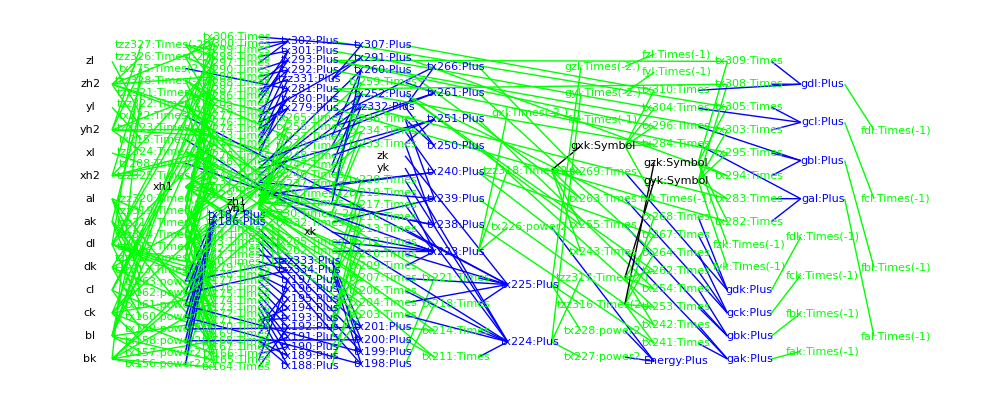

```mathematica
packGraph[staplePack]
```